## Single Pendulum

```mathematica
SinglePendulum[w_, v0_, tmax_] := Module[{s, y,t},
s = NDSolve[{Sin[y[t]]+ w y''[t]==0, y[0]==0, y'[0]== v0}, y, {t, 0, tmax}];
Function[t, y[t] /. s]]
```

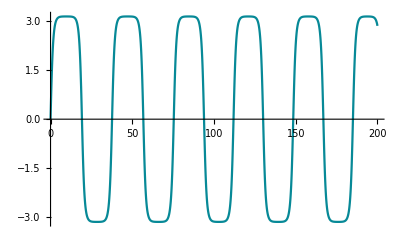

```mathematica
Plot[SinglePendulum[1, 1.9999999,200][x],{x,0,200},PlotRange->All]
```